```mathematica
k =(1-r)^10*(429*r^4+450*r^3+210*r^2+50*r+5)
k=TransformedField["Polar"->"Cartesian",k,{r,θ}->{x,y}]
```

(1-r)^10 (5+50 r+210 r^2+450 r^3+429 r^4)

(-1+√(x^2+y^2))^10 (5+210 x^2+429 x^4+210 y^2+858 x^2 y^2+429 y^4+50 √(x^2+y^2)+450 x^2 √(x^2+y^2)+450 y^2 √(x^2+y^2))

1/(√(x^2+y^2))26 x (-1+√(x^2+y^2))^9 (231 x^4+5 √(x^2+y^2)+3 y^2 (15+77 y^2+53 √(x^2+y^2))+3 x^2 (15+154 y^2+53 √(x^2+y^2)))

(26 r (-1+√(r^2))^9 (45 r^2+231 r^4+√(r^2) (5+159 r^2)) Cos[θ])/(√(r^2))

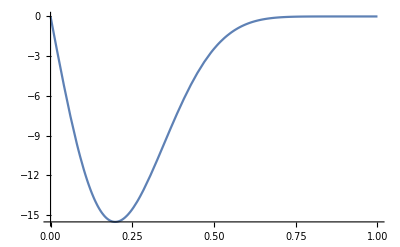

1/(√(x^2+y^2))26 y (-1+√(x^2+y^2))^9 (231 x^4+5 √(x^2+y^2)+3 y^2 (15+77 y^2+53 √(x^2+y^2))+3 x^2 (15+154 y^2+53 √(x^2+y^2)))

(26 r (-1+√(r^2))^9 (45 r^2+231 r^4+√(r^2) (5+159 r^2)) Sin[θ])/(√(r^2))

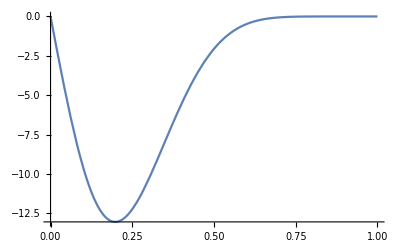

```mathematica
gradkx=FullSimplify[D[k,x]]
gradkxrad=FullSimplify[TransformedField["Cartesian"->"Polar",gradkx,{x,y}->{r,θ}]]
Plot[gradkxrad/.{θ->0},{r,0,1},PlotRange->Full]
gradky=FullSimplify[D[k,y]]
gradkyrad=FullSimplify[TransformedField["Cartesian"->"Polar",gradky,{x,y}->{r,θ}]]
Plot[gradkyrad/.{θ->1},{r,0,1},PlotRange->Full]
```

{{-1/(√(x^2+y^2))26 (-1+√(x^2+y^2))^8 (-5 √(x^2+y^2)+2 y^2 (-20+9 √(x^2+y^2))+3 x^4 (-24+77 √(x^2+y^2))+y^4 (984+3003 √(x^2+y^2))+2 x^2 (-20-57 √(x^2+y^2)+3 y^2 (152+539 √(x^2+y^2)))),(3432 x y (-1+√(x^2+y^2))^8 (√(x^2+y^2)+x^2 (8+21 √(x^2+y^2))+y^2 (8+21 √(x^2+y^2))))/(√(x^2+y^2))},{(3432 x y (-1+√(x^2+y^2))^8 (√(x^2+y^2)+x^2 (8+21 √(x^2+y^2))+y^2 (8+21 √(x^2+y^2))))/(√(x^2+y^2)),-1/(√(x^2+y^2))26 (-1+√(x^2+y^2))^8 (-5 √(x^2+y^2)-2 y^2 (20+57 √(x^2+y^2))+3 y^4 (-24+77 √(x^2+y^2))+x^4 (984+3003 √(x^2+y^2))+2 x^2 (-20+9 √(x^2+y^2)+3 y^2 (152+539 √(x^2+y^2))))}}

{{(26 (-1+√(r^2))^8 (40 r^2+√(r^2) (5+114 r^2)+r^4 (72-231 √(r^2))))/(√(r^2)),0},{0,-(26 (-1+√(r^2))^8 (-40 r^2+√(r^2) (-5+18 r^2)+r^4 (984+3003 √(r^2))))/(√(r^2))}}

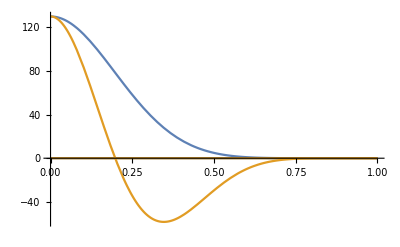

```mathematica
kij=FullSimplify[({{-D[D[k,y],y], D[D[k,x],y]}, {D[D[k,y],x], -D[D[k,x],x]}})]
krad=FullSimplify[TransformedField["Cartesian"->"Polar",kij,{x,y}->{r,θ}]]
Plot[krad,{r,0,1},PlotRange->Full]
```

{{1/(√(x^2+y^2))3432 x (-1+√(x^2+y^2))^7 (-21 x^4-231 y^4+√(x^2+y^2)+y^2 (7-17 √(x^2+y^2))+x^2 (7-252 y^2+13 √(x^2+y^2))),-1/(√(x^2+y^2))3432 y (-1+√(x^2+y^2))^7 (-231 x^4-21 y^4+√(x^2+y^2)+x^2 (7-252 y^2-17 √(x^2+y^2))+y^2 (7+13 √(x^2+y^2)))},{-1/(√(x^2+y^2))3432 y (-1+√(x^2+y^2))^7 (-231 x^4-21 y^4+√(x^2+y^2)+x^2 (7-252 y^2-17 √(x^2+y^2))+y^2 (7+13 √(x^2+y^2))),1/(√(x^2+y^2))10296 x (-1+√(x^2+y^2))^7 (-91 x^4-21 y^4+√(x^2+y^2)+x^2 (7-112 y^2+3 √(x^2+y^2))+y^2 (7+13 √(x^2+y^2)))}}

{{(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Cos[θ])/(√(r^2)),(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Sin[θ])/(√(r^2))},{(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Sin[θ])/(√(r^2)),(10296 r (-1+√(r^2))^7 (7 r^2-91 r^4+√(r^2) (1+3 r^2)) Cos[θ])/(√(r^2))}}

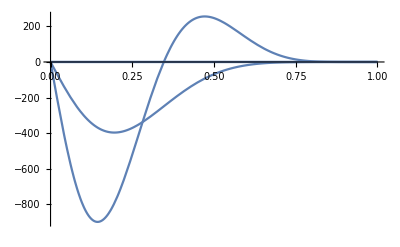

```mathematica
diffx=FullSimplify[D[kij,x]]
diffxrad=FullSimplify[TransformedField["Cartesian"->"Polar",diffx,{x,y}->{r,θ}]]
Plot[diffxrad/.{θ->0},{r,0,1},PlotRange->Full]
```

{{1/(√(x^2+y^2))10296 y (-1+√(x^2+y^2))^7 (-21 x^4-91 y^4+√(x^2+y^2)+y^2 (7+3 √(x^2+y^2))+x^2 (7-112 y^2+13 √(x^2+y^2))),-1/(√(x^2+y^2))3432 x (-1+√(x^2+y^2))^7 (-21 x^4-231 y^4+√(x^2+y^2)+y^2 (7-17 √(x^2+y^2))+x^2 (7-252 y^2+13 √(x^2+y^2)))},{-1/(√(x^2+y^2))3432 x (-1+√(x^2+y^2))^7 (-21 x^4-231 y^4+√(x^2+y^2)+y^2 (7-17 √(x^2+y^2))+x^2 (7-252 y^2+13 √(x^2+y^2))),1/(√(x^2+y^2))3432 y (-1+√(x^2+y^2))^7 (-231 x^4-21 y^4+√(x^2+y^2)+x^2 (7-252 y^2-17 √(x^2+y^2))+y^2 (7+13 √(x^2+y^2)))}}

{{(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Sin[θ])/(√(r^2)),-(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Cos[θ])/(√(r^2))},{-(3432 r (-1+√(r^2))^7 (7 r^2-21 r^4+√(r^2) (1+13 r^2)) Cos[θ])/(√(r^2)),(10296 r (-1+√(r^2))^7 (7 r^2-91 r^4+√(r^2) (1+3 r^2)) Sin[θ])/(√(r^2))}}

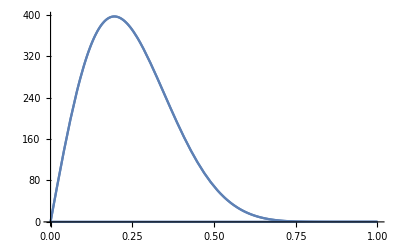

```mathematica
diffy = FullSimplify[D[kij,y]]
diffyrad=FullSimplify[TransformedField["Cartesian"->"Polar",diffy,{x,y}->{r,θ}]]
Plot[diffyrad/.{θ->0},{r,0,1},PlotRange->Full]
```

{{-1/(√(x^2+y^2))6864 (-1+√(x^2+y^2))^6 (2 √(x^2+y^2)+y^2 (12-93 √(x^2+y^2))+x^4 (-158+147 √(x^2+y^2))+y^4 (-698+1617 √(x^2+y^2))+x^2 (-3 (-4+√(x^2+y^2))+4 y^2 (-214+441 √(x^2+y^2)))),1/(√(x^2+y^2))205920 x y (-1+√(x^2+y^2))^6 (-3 √(x^2+y^2)+x^2 (-18+49 √(x^2+y^2))+y^2 (-18+49 √(x^2+y^2)))},{1/(√(x^2+y^2))205920 x y (-1+√(x^2+y^2))^6 (-3 √(x^2+y^2)+x^2 (-18+49 √(x^2+y^2))+y^2 (-18+49 √(x^2+y^2))),-1/(√(x^2+y^2))6864 (-1+√(x^2+y^2))^6 (2 √(x^2+y^2)-3 y^2 (-4+√(x^2+y^2))+y^4 (-158+147 √(x^2+y^2))+x^4 (-698+1617 √(x^2+y^2))+x^2 (12-93 √(x^2+y^2)+4 y^2 (-214+441 √(x^2+y^2))))}}

{{(6864 (-1+√(r^2))^6 (-12 r^2+√(r^2) (-2+3 r^2)+r^4 (158-147 √(r^2))))/(√(r^2)),0},{0,(6864 (-1+√(r^2))^6 (-12 r^2+√(r^2) (-2+93 r^2)+r^4 (698-1617 √(r^2))))/(√(r^2))}}

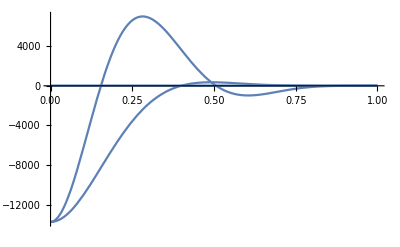

```mathematica
laplace=FullSimplify[D[D[kij,x],x]+D[D[kij,y],y]]
laplacerad=FullSimplify[TransformedField["Cartesian"->"Polar",laplace,{x,y}->{r,θ}]]
Plot[laplacerad/.{θ->0},{r,0,1},PlotRange->Full]
```

```mathematica
(1-√(x^2+y^2))^10 (5+50 √(x^2+y^2)+210 (x^2+y^2)+450 (x^2+y^2)^(3/2)+429 (x^2+y^2)^2)
```

(1-√(x^2+y^2))^10 (5+50 √(x^2+y^2)+210 (x^2+y^2)+450 (x^2+y^2)^(3/2)+429 (x^2+y^2)^2)

```mathematica
l
```